```mathematica
(*PSO 20 particles, 100 iterations*)
data1={0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3311000000000235,0.3311000000003633,0.33110000000772666,0.3311000000000046,0.3311000000050604,0.3311000000003207,0.33110000000000916,0.33110000000001394,0.33110000000000456,0.33110000000376394,0.3311000000159755,0.33110000000032175};
```

```mathematica
{Mean[data1],Median[data2],Median[data3]}
```

{0.3311,0.3311,0.3311}

```mathematica
(*PSO 20 particles, 500 iterations*)
data2 = {0.33109999999999984,0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3310999999999998,0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3310999999999998,0.3310999999999999,0.3311,0.33109999999999984,0.33109999999999984,0.33109999999999984,0.3311000000000085};
```

```mathematica
StandardDeviation[data1]
```

4.47073×10^-12

```mathematica
StandardDeviation[data2]
```

2.2328×10^-15

```mathematica
StandardDeviation[data1](*StdDev for 20np 100nit*)
```

4.47073×10^-12

```mathematica
StandardDeviation[data2](*StdDev for 20np 500nit*)
```

2.60506×10^-15

```mathematica
(*PSO 40 particles, 100 iterations*)data3 = {0.3311000000024352,0.33110000001074713,0.3311000000000046,0.33110000000082634,0.3311000000002402,0.3311000000001075,0.33110000022497593,0.3311000000000255,0.3310999999999999,0.3310999999999999,0.3311};
```

```mathematica
StandardDeviation[data3](*StdDev for 40np 100nit*)
```

6.74743×10^-11

```mathematica
data4=Flatten[Import["~/Desktop/Uni\ shizz\ 4th\ year/CS4525\ Project/Haskell/ghc-eden-7.6.1/testing2.txt","Data"]]

Sort[{0.3310999999999999,0.33109999999999984,0.33109999999999984,0.3311000000000235,0.3311000000003633,0.33110000000772666,0.3311000000000046,0.3311000000050604,0.3311000000003207,0.33110000000000916,0.33110000000001394,0.33110000000000456,0.33110000000376394,0.3311000000159755,0.33110000000032175},Less]
```

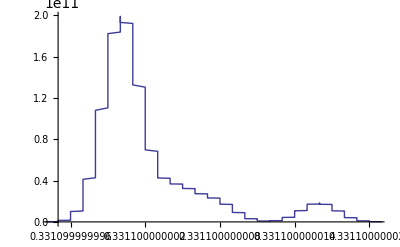

```mathematica
SmoothHistogram[data1,Automatic,"PDF"]
```

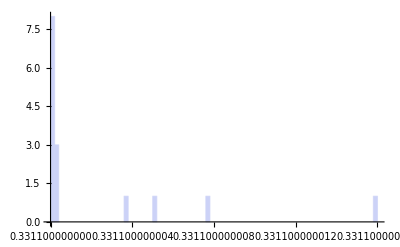

```mathematica
Histogram[data1,100]
```

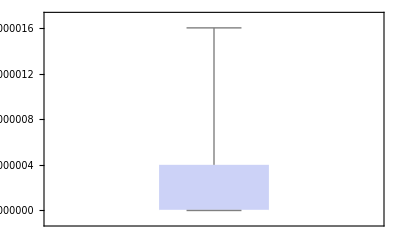

```mathematica
BoxWhiskerChart[data1]
```

```mathematica
(*Following is the data for testPSO.txt which tests constriction factors.*)
```

```mathematica
data21 = {0.9140999999999991,0.9140999999999992,0.9140999999999991,0.9140999999999995,0.9140999999999996,0.9140999999999992,0.9140999999999992,0.9140999999999992,0.9140999999999992,0.9140999999999992,0.914099999999999,0.9140999999999991,0.9140999999999992,0.9140999999999989,0.9140999999999992,0.9140999999999991,0.9140999999999995,0.9140999999999994,0.9140999999999994,0.914099999999999}
StandardDeviation[data1]
```

{0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141}

1.61088×10^-16

```mathematica
data22={0.914099999999999,0.9140999999999989,0.914099999999999,0.9140999999999992,0.914099999999999,0.9140999999999992,0.9140999999999989,0.9140999999999991,0.914099999999999,0.914099999999999,0.9140999999999994,0.914099999999999,0.9140999999999989,0.9140999999999989,0.9140999999999991,0.9140999999999992,0.9140999999999995,0.9140999999999991,0.9140999999999989,0.9140999999999989}
StandardDeviation[data22]
```

{0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141}

1.72748×10^-16

```mathematica
data23={0.9141001344878226,0.9141020842615248,0.9141010076244758,0.9141000114198997,0.9141000103020339,0.9141024297655886,0.9141007738801588,0.9141000259586043,0.9141018344721783,0.9141014994960018,0.9141003050067964,0.9141010556811353,0.9141062103584059,0.9141031410691673,0.914102377844142,0.914124441556149,0.9141000006683239,0.914102199493055,0.9141043312183866,0.9141004708536062}
StandardDeviation[data23]
```

{0.9141,0.914102,0.914101,0.9141,0.9141,0.914102,0.914101,0.9141,0.914102,0.914101,0.9141,0.914101,0.914106,0.914103,0.914102,0.914124,0.9141,0.914102,0.914104,0.9141}

5.36229×10^-6

```mathematica
data24={0.9141411881129956,0.9142005342311976,0.9141141171255334,0.9141867837565565,0.9141239752730616,0.9142431378146977,0.914137262801665,0.9141572395703302,0.9142355194539499,0.9141577443834252,0.9141662114223291,0.9141690348891207,0.9141737318170899,0.9141566270443193,0.9141062723726792,0.9141166773383033,0.9141792857146174,0.9141342099643939,0.9141067710143833,0.9141320715810547}
StandardDeviation[data24]
```

{0.914141,0.914201,0.914114,0.914187,0.914124,0.914243,0.914137,0.914157,0.914236,0.914158,0.914166,0.914169,0.914174,0.914157,0.914106,0.914117,0.914179,0.914134,0.914107,0.914132}

0.0000389374

```mathematica
data25={0.914207596085302,0.91410321295459,0.9141196037619853,0.9142050979079516,0.9141245974709327,0.9141354420720601,0.9141424308495572,0.9141562583836846,0.9141046285841078,0.914105964764435,0.9142182359110826,0.9141383751330914,0.9141581541960425,0.9141123639329142,0.9141030261707,0.9141809343286167,0.9141866887778222,0.9142579749158725,0.9141140927277053,0.9141606396285045}
StandardDeviation[data25]
```

{0.914208,0.914103,0.91412,0.914205,0.914125,0.914135,0.914142,0.914156,0.914105,0.914106,0.914218,0.914138,0.914158,0.914112,0.914103,0.914181,0.914187,0.914258,0.914114,0.914161}

0.0000448388

```mathematica
data26={0.9140999999999992,0.9140999999999995,0.914099999999999,0.9140999999999992,0.914099999999999,0.914099999999999,0.9140999999999991,0.9140999999999987,0.9140999999999995,0.9140999999999988,0.9140999999999991,0.9140999999999991,0.914099999999999,0.9140999999999991,0.9140999999999996,0.9140999999999992,0.9140999999999994,0.9140999999999985,0.9140999999999996,0.9140999999999991}
StandardDeviation[data26]
```

{0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141,0.9141}

2.81328×10^-16

```mathematica
(*Scalability*)
scal1={0.3961000000000924,0.39610005762475775,0.3961000037182159,0.3961000000329766,0.3961000000000106,0.3961000000792122,0.3961000000050603,0.39610000081044017,0.3960999999999998,0.39610000000005324,0.3960999999999999,0.39610000000040896,0.39610000120907946,0.3961000000241184,0.39610000000003465,0.3961000020457903,0.39610000000001394,0.396100000000115,0.3961000000001395};
scal2={0.3960999999999999,0.39609999999999995,0.39609999999999984,0.39609999999999984,0.3960999999999999,0.3961000000000115,0.39609999999999984,0.3960999999999999,0.39609999999999984,0.39609999999999995,0.39609999999999973,0.39609999999999984,0.3960999999999999,0.39609999999999984,0.3960999999999999,0.39609999999999984,0.39609999999999984};
scal3={0.3961000000000139,0.39610000057968475,0.3961000000021974,0.39610000000001916,0.39610000000559836,0.39610000000000317,0.39610000004825263,0.39610000000002565,0.39610000023907305,0.39610000000989404,0.39610000000000745,0.39609999999999995,0.3961000000003067,0.39610000000025863,0.396100000000115,0.3960999999999999};
scal4={0.47260000000001146,0.4726000000001279,0.47260000000002095,0.4726000000000021,0.4726002472739108,0.47260000000024094,0.4726000218695227,0.4726000002342501,0.47260000000278374,0.4726000865208052,0.4726000000000137,0.4726000000137893,0.47260000000001623,0.47260000095407373,0.47260000624865295,0.4726000001725963,0.47260000000000524,0.4726000000054226};
scal5={0.4725999999999998,0.47260000000009916,0.4725999999999998,0.47259999999999985,0.4725999999999999,0.47259999999999974,0.47259999999999985,0.4725999999999998,0.47259999999999974,0.47259999999999985,0.47259999999999985,0.47259999999999985,0.4725999999999998,0.4726000000000395,0.4726000000000011,0.47259999999999985,0.4725999999999998,0.4726000000000045};
scal6={0.47259999999999985,0.47260000008571706,0.47260000000001995,0.4726000000000047,0.4726000000016493,,0.4725999999999998,,0.4726000000000092,0.4726000000000001,0.4725999999999998,,0.4726000000000021,0.4726000000026210,,0.4726000000059122,0.4726000000000095,0.4725999999999999,0.4725999999999998,,0.4726000000161839,,0.47260000000021446,0.4726000005198801};
scal7={0.9141000000059598,0.9141000000027897,0.9141000000000056,0.9141000000001204,0.9141000000024967,0.9141000000000075,0.9141000000000019,0.9141000001861994,0.9141001626670786,0.9141000070811482,0.9141000000012074,0.9141000002584102};
scal8={0.9140999999999992,0.9140999999999995,0.9141000008561049,0.9140999999999996,0.914100000004725,0.9140999999999998,0.9140999999999994,0.9140999999999991,0.9140999999999992,0.9140999999999995,0.9140999999999996,0.9140999999999995,0.9140999999999992,0.9140999999999996,0.9140999999999996,0.9140999999999991,0.9140999999999998};
scal9={0.9141000000000071,0.9141000107810803,0.9141000000000195,0.9141000000000008,0.9141000000007615,0.9141000000000074,0.9141000000032209,0.9141000000005889,0.914100000000028,0.9141000000000635,0.9141000000031436,0.9140999999999995,0.9141000000000027,0.9140999999999997,0.9141000004221771};
{StandardDeviation[scal1],StandardDeviation[scal2],StandardDeviation[scal3],StandardDeviation[scal4],StandardDeviation[scal5],StandardDeviation[scal6],StandardDeviation[scal7],StandardDeviation[scal8],StandardDeviation[scal9]}
```

{1.31542×10^-8,2.82194×10^-15,1.5202×10^-10,6.03013×10^-8,2.46128×10^-14,1/(√23)(√(4 Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+Abs[0.4726+1/24 (-8.5068-6 Null)]^2+6 Abs[1/24 (-8.5068-6 Null)+Null]^2)),4.68039×10^-8,2.07568×10^-10,2.77785×10^-9}

```mathematica
sum1={1.0000000000000089,0.9999999939936045,0.9999999996124396,0.9999999999965627,0.9999999999999989,0.9999999999917435,1.0000000000004863,1.0000000000778813,1.0,0.9999999999999944,1.0,1.0000000000000393,0.9999999998739741,1.0000000000023177,1.0000000000000033,0.9999999997867614,1.0000000000000013,0.999999999999988,0.9999999999999855};
sum11={1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
sum2={1.0000000000000013,0.9999999999395778,1.0000000000002112,0.999999999999998,0.9999999999994165,0.9999999999999997,1.000000000004637,0.9999999999999973,0.9999999999750807,0.9999999999989687,0.9999999999999992,1.0,0.999999999999968,1.0000000000000249,0.999999999999988,1.0};
sum3={0.9999999999999988,1.0000000000000122,0.9999999999999978,0.9999999999999998,0.999999974018754,0.9999999999999747,1.000000002086269,1.0000000000223466,1.0000000000002656,0.9999999909091973,0.9999999999999986,0.9999999999985512,1.0000000000000016,1.000000000091015,1.0000000005960976,0.9999999999818652,0.9999999999999994,0.9999999999994302};
sum4={1.0,0.9999999999999896,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0000000000000038,0.9999999999999999,1.0,1.0,1.0};
sum5={1.0,0.9999999999909936,0.9999999999999979,1.0000000000000004,0.9999999999998267,1.0,1.0000000000000009,1.0,1.0,0.9999999999999998,1.00000000000025,1.000000000000564,0.999999999999999,1.0,1.0,1.0000000000015439,1.0000000000000204,0.9999999999453758};
sum6={1.0000000000005456,1.1,1.0000000000002554,0.9999999999999993,0.9999999999999868,0.9999999999997249,1.0000000000000007,0.9999999999999998,0.9999999999794842,1.0000000148906618,0.9999999992197856,0.999999999999867,1.000000000023655};
sum7={1.0,1.0,0.9999999999056727,1.0,0.9999999999994793,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0,1.0};
sum8={0.9999999999999991,1.0000000009869079,1.0000000000000018,0.9999999999999999,0.9999999999999161,1.0000000000000007,0.9999999999996451,0.999999999999935,0.9999999999999969,0.999999999999993,1.0000000000002878,1.0,1.0000000000000002,1.0,1.0000000000386464};
{StandardDeviation[sum1],StandardDeviation[sum11],StandardDeviation[sum2],StandardDeviation[sum3],StandardDeviation[sum4],StandardDeviation[sum5],StandardDeviation[sum6],StandardDeviation[sum7],StandardDeviation[sum8]}
```

{1.3735×10^-9,0.,1.60689×10^-11,6.4372×10^-9,2.66467×10^-15,1.29662×10^-11,0.027735,2.28702×10^-11,2.54305×10^-10}

```mathematica
time1={0.039712,0.041968,0.044316,0.043766,0.053435,0.043619,0.052551,0.041274,0.049465,0.048899,0.055175,0.042393,0.040186,0.049775,0.050936,0.041351,0.043837,0.048421,0.050421};
time2={0.109414,0.125016,0.10036,0.123643,0.110227,0.107601,0.103555,0.102506,0.111844,0.105204,0.122921,0.09935,0.090957,0.101743,0.103611,0.104097,0.107703};
time3={0.072602,0.081561,0.082166,0.087863,0.074584,0.084842,0.076658,0.094317,0.07643,0.082334,0.07606,0.079949,0.080951,0.084864,0.083837,0.080927};
time4={0.053057,0.051095,0.05191,0.059413,0.061147,0.064877,0.052941,0.050784,0.057223,0.050196,0.052862,0.05362,0.050269,0.055841,0.057831,0.066586,0.053134,0.057903};
time5={0.138051,0.124046,0.130943,0.131791,0.11403,0.119566,0.114919,0.131096,0.121893,0.135621,0.131695,0.124918,0.125556,0.12029,0.118601,0.129254,0.124684,0.118445};
time6={0.11259,0.108534,0.106935,0.103573,0.1043,0.098924,0.108024,0.106778,0.102443,0.099096,0.09607,0.106065,0.116893,0.105647,0.102165,0.106984,0.124326,0.101661};
time7={0.089132,0.083944,0.087179,0.088726,0.08413,0.084993,0.093863,0.091052,0.090609,0.080679,0.079843,0.089229,0.114063};
time8={0.177709,0.182802,0.183269,0.170559,0.202475,0.192321,0.178712,0.181771,0.192346,0.174813,0.180422,0.173567,0.171809,0.175672,0.187595,0.182597,0.180392};
time9={0.176422,0.177436,0.171536,0.180584,0.174209,0.178223,0.169738,0.171122,0.169962,0.179648,0.167347,0.183027,0.165125,0.167165,0.178913};
{StandardDeviation[time1],StandardDeviation[time2],StandardDeviation[time3],StandardDeviation[time4],StandardDeviation[time5],StandardDeviation[time6],StandardDeviation[time7],StandardDeviation[time8],StandardDeviation[time9]}
```

{0.00487954,0.00912289,0.00542592,0.00491575,0.00699414,0.00669427,0.00856579,0.00828043,0.00557404}

```mathematica
{Mean[time1],Mean[time2],Mean[time3],Mean[time4],Mean[time5],Mean[time6],Mean[time7],Mean[time8],Mean[time9]}
```

{0.0463947,0.107632,0.0812466,0.0555938,0.1253,0.106167,0.089034,0.181696,0.17403}